(2 π)/ω

2 π

{{0,2/π},{1,0},{2,-2/(3 π)},{3,0},{4,-2/(15 π)},{5,0},{6,-2/(35 π)},{7,0},{8,-2/(63 π)},{9,0},{10,-2/(99 π)},{11,0},{12,-2/(143 π)},{13,0},{14,-2/(195 π)},{15,0},{16,-2/(255 π)},{17,0},{18,-2/(323 π)},{19,0},{20,-2/(399 π)}}

{{0,0},{1,1/2},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0}}

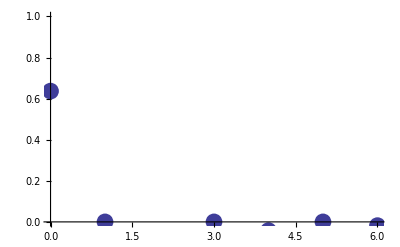

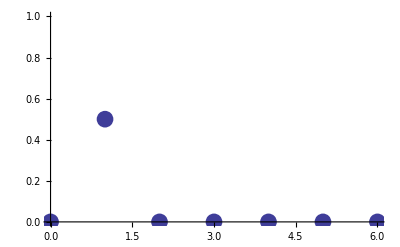

Part::pspec: Part specification i is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

1/π+∑_(i=2)^n (Cos[2 π t {{0,2/π},{1,0},{2,-2/(3 π)},{3,0},{4,-2/(15 π)},{5,0},{6,-2/(35 π)},{7,0},{8,-2/(63 π)},{9,0},{10,-2/(99 π)},{11,0},{12,-2/(143 π)},{13,0},{14,-2/(195 π)},{15,0},{16,-2/(255 π)},{17,0},{18,-2/(323 π)},{19,0},{20,-2/(399 π)}}⟦i,1⟧] {{0,2/π},{1,0},{2,-2/(3 π)},{3,0},{4,-2/(15 π)},{5,0},{6,-2/(35 π)},{7,0},{8,-2/(63 π)},{9,0},{10,-2/(99 π)},{11,0},{12,-2/(143 π)},{13,0},{14,-2/(195 π)},{15,0},{16,-2/(255 π)},{17,0},{18,-2/(323 π)},{19,0},{20,-2/(399 π)}}⟦i,2⟧+{{0,0},{1,1/2},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0}}⟦i,2⟧ Sin[2 π t {{0,0},{1,1/2},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0}}⟦i,1⟧])

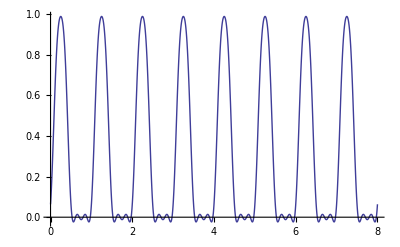

```mathematica
Remove["Global`*"]
(*parameters*)
T=2 π/ω
ω=2 π

(*periodic impulse*)
F[t_]=Sin[ω t]; (*0 < t < π/ω*)

(*coefficients *)
a[n_]:=2/T Integrate[F[t] Cos[n ω t],{t,0,π/ω}];
b[n_]:=2/T Integrate[F[t] Sin[n ω t],{t,0,π/ω}];
alist=Table[{n,a[n]},{n,0,20}]
blist=Table[{n,b[n]},{n,0,20}]
plota:=ListPlot[alist,PlotStyle->PointSize[.03],PlotRange->{{0,6},{0,1}}]
plotb:=ListPlot[blist,PlotStyle->PointSize[.03],PlotRange->{{0,6},{0,1}}]
func[n_,t_]=alist[[1,2]]/2 + Sum[alist[[i,2]] Cos[alist[[i,1]] ω t]+blist[[i,2]] Sin[blist[[i,1]] ω t],{i,2,n}]
Plot[func[5,t],{t,0,8},PlotRange->All]
```